```mathematica
(* applosses4.nb Will Saunders AAO Jan 2013. *)
(* 1) Sets up approximation for convolved profile for site seeing with Moffat β=3.5 profile, exponential or deVaucouleurs R^1/4 image profiles, and Gaussian image degradation from spot sizes, guiding erros, dome/telescope seeing, deviations from ideal optics etc. 
The approximation assumes a Moffat profile for the convolved profile, with β and R chosen to give the correct central surface brightness and 2nd moment. *)
(* 2) Calculates aperture losses for this profile for circular apertures, including any offset from the image center. *)
(* 3) Estimates relative S/N at Zenith, assuming sky-limited observations, and including a factor for intrinsic spectral PSF degradation in the sperctrograph due to the finite fiber size. Plots and maximises S/N for various image types and parameters as a function of fiber size. *)
(* 4) calculates the differential refraction for arbitrary ZD and pair of wavelengths, according to ESO formula for LaSilla. Also the sky brightness and extinction as a fucnction of AM. *)
(* 5) Using SDSS AM distn, finds overall survey time to a fixed S/N for all target types,  tests these numbers for robsutness, and determines scalings between the input parameters and fiber size and survey time.*)
(* 6) Examines effect of ADC on survey time, including throughut derived from SK's ADC design.*) 
(* To be read in conjunction with technical note 'DESpec_ADC_aperture_survey_speed', WS 1/2013 *)
```

```mathematica
(* Set up Moffat PSF *)
```

```mathematica
Moff[r_,R_,β_]:=(β-1)/(Pi R^2(1 + (r/R)^2)^β)
```

```mathematica
NIntegrate[2 Pi r Moff[r,1.2345,3.5567],{r,0,Infinity}]
```

1.

```mathematica
Rhwhm35=r/.FindRoot[Moff[r, 1.,3.5] == Moff[0., 1.,3.5]/2, {r, .5}] (* find HWHM *)
```

0.467989

```mathematica
Integrate[2 Pi r r^2Moff[r,1,β],{r,0,Infinity},Assumptions->Re[β]>2]
```

1/(-2+β)

```mathematica
MoffM2[r_,RM_,β_]:=(β-1)/(Pi (β-2)RM^2(1 + (r/RM)^2/(β-2))^β)
```

```mathematica
(* so for MoffM2, M2 = RM^2 always *)
```

```mathematica
NIntegrate[2 Pi r r^2MoffM2[r,1.2345,3.5678]/1.2345^2,{r,0,Infinity}]
```

1.

```mathematica
MoffM2[0,RM,β]
```

(-1+β)/(π RM^2 (-2+β))

```mathematica
R2HWWM35=r/.FindRoot[MoffM2[r, 1.,3.5] == MoffM2[0., 1.,3.5]/2, {r, .5}] (* find HWHM *)
```

0.573167

```mathematica
(* so HWHM is 0.573167 R  *)
```

```mathematica
HWHM2R35=1/R2HWWM35
```

1.74469

```mathematica
Moff35h[r_,Rhwhm_]:=5 Rhwhm^2/(2Pi)/Rhwhm35^2 (1 + (Rhwhm35 r/Rhwhm)^2)^(-3.5)
```

```mathematica
(* Moff35h is a Moffat profile with beta=3.5, defined by its half-width at half height *)
```

```mathematica
Moff35h[1,1]/ Moff35h[0,1]
```

0.5

```mathematica
FindRoot[Integrate[2 Pi r r^2 Moff35h[r,1],{r,0,Ref}]==0.5,{Ref,1}]
```

{Ref→1.44585}

```mathematica
MM2 =Integrate[2 Pi r r^2 Moff35h[r,1],{r,0,Infinity}]
```

3.04395

```mathematica
(* So the 2nd moment of Moff35[r,Rhwhm] is 3.044 Rhwhm^2 *)
```

```mathematica
(* Now exponential profile *)
```

```mathematica
ae=r/.FindRoot[(1+r) Exp[-r]==0.5,{r,1}]
```

1.67835

```mathematica
Integrate[ae^2r  Exp[-ae r],{r,0,1}]
```

0.5

```mathematica
EProf[r_,Re50_]:=1/(2Pi) (ae/Re50)^2Exp[-ae r/ Re50]
```

```mathematica
Integrate[2 Pi r EProf[r,1],{r,0,Infinity}]
```

1.

```mathematica
FindRoot[Integrate[2 Pi r  EProf[r,1],{r,0,Ref}]==0.5,{Ref,1}]
```

{Ref→1.}

```mathematica
FindRoot[EProf[Rhm,1]/EProf[0,1]==.5,{Rhm,1}]
```

{Rhm→0.412994}

```mathematica
ME2=Integrate[2 Pi r r^2 EProf[r,1],{r,0,Infinity}]
```

2.13004

```mathematica
(* So the 2nd moments of EProf[r,Ref] is 2.13004Ref^2 *)
```

```mathematica
(* Now de Vaucouleurs r^1/4 profile  *)
```

```mathematica
VProft[r_,Re50_]:=(1/Re50)^2 Exp[-(r/Re50)^0.25]
```

```mathematica
KV=Integrate[2 Pi r VProft[r,Ref],{r,0,Infinity},Assumptions->Re[Ref^0.25]>0]
```

126669.

```mathematica
VProft[r_,Re50_]:=(1/Re50)^2/KV Exp[-(r/Re50)^0.25]
```

```mathematica
Integrate[2 Pi r VProft[r,Ref],{r,0,Infinity},Assumptions->Re[Ref^0.25]>0]
```

1.

```mathematica
Reft=Ref/.FindRoot[Integrate[2 Pi r  VProft[r,1],{r,0,Ref}]==0.5,{Ref,1}]
```

3459.49

```mathematica
VProf[r_,Re50_]:=(Reft/Re50)^2/KV Exp[-(Reft r/Re50)^0.25]
```

```mathematica
Integrate[2 Pi r VProf[r,Ref],{r,0,Infinity},Assumptions->Re[Ref^0.25]>0]
```

1.

```mathematica
FindRoot[Integrate[2 Pi r  VProf[r,1.2345],{r,0,Ref}]==0.5,{Ref,1}]
```

{Ref→1.2345}

```mathematica
MV2=Integrate[2 Pi r r^2 VProf[r,1],{r,0,Infinity}]
```

21.6793

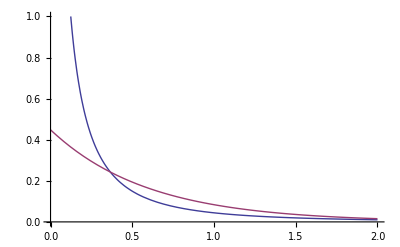

```mathematica
Plot[{VProf[r,1],EProf[r,1]},{r,0,2},PlotRange->{0,1}]
```

```mathematica
Integrate[2 Pi r VProf[r,1.2345],{r,0,1.2345},Assumptions->Re[Ref^0.25]>0]
```

0.5

```mathematica
Integrate[2 Pi r EProf[r,1.2345],{r,0,1.2345},Assumptions->Re[Ref^0.25]>0]
```

0.5

```mathematica
EProf[0,1]
```

0.448315

```mathematica
VProf[0,1]
```

94.4827

```mathematica
(* Now Gaussian profile *)
```

```mathematica
GProf[r_,Rrms_]:=1/(Pi Rrms^2  Exp[(r/Rrms)^2])
```

```mathematica
Integrate[2 Pi r GProf[r,1.2345],{r,0,Infinity}]
```

1.

```mathematica
FindRoot[Integrate[2 Pi r GProf[r,1],{r,0,Reff}]==.5,{Reff,1}]
```

{Reff→0.832555}

```mathematica
FindRoot[GProf[rhwhm,1]==GProf[0,1]/2,{rhwhm,1}]
```

{rhwhm→0.832555}

```mathematica
Sqrt[Integrate[2 Pi r r^2GProf[r,1.2345],{r,0,Infinity}]]
```

1.2345

```mathematica
MG2=Integrate[2 Pi r r^2GProf[r,1],{r,0,Infinity}]
```

1

```mathematica
MMEVG2[Rhwhm_,RefE_,RefV_,Rrms_]:= MM2 Rhwhm^2 + ME2 RefE^2 +MV2 RefV^2+ MG2 Rrms^2
```

```mathematica
(* 2nd moment of convolved profile  *)
```

```mathematica
MEVG0[Rhwhm_,RefE_,RefV_,Rrms_]:=If[RefE RefV!=0,Print["Ooops RE OR RV please"],
If[RefE==0&&RefV==0,MG0[Rhwhm,Rrms],If[RefV==0,NIntegrate[2Pi r MoffM2[Sqrt[r^2+rt^2-2 r rt Cos[th]],1.7446920204827057Rhwhm ,3.5]2  rt GProf[rt,Rrms]EProf[r,RefE],{th,0, Pi},{rt,0,3Rrms},{r,0,5RefE},AccuracyGoal->3],NIntegrate[2Pi r MoffM2[Sqrt[r^2+rt^2-2 r rt Cos[th]],1.7446920204827057Rhwhm ,3.5]2  rt GProf[rt,Rrms]VProf[r,RefV],{th,0, Pi},{rt,0,3Rrms},{r,0,5RefV},AccuracyGoal->3] ]  ]]
```

```mathematica
(* MEVG0 is the value of the MEG or MVG convolution at the origin *)
```

```mathematica
MEVG0[1,1,1,1]
```

Ooops RE OR RV please

```mathematica
MEVG0[1,.5,0.,.5]
```

0.11627

```mathematica
MEVG0[1,0,0.5,.5]
```

0.101294

```mathematica
MEVG0[1,0,0,.5]
```

0.147264

```mathematica
BetaMEVG0[Rhwhm_,RefE_,RefV_,Rrms_]:=(2 Pi MEVG0[Rhwhm,RefE,RefV,Rrms]MMEVG2[Rhwhm,RefE,RefV,Rrms]-1)/( Pi MEVG0[Rhwhm,RefE,RefV,Rrms]MMEVG2[Rhwhm,RefE,RefV,Rrms]-1)
```

```mathematica
BetaMEVG0[.5,0,0,.25]
```

3.90866

```mathematica
MGProf[r_,Rhwhm_,Rrms_]:=NIntegrate[MoffM2[Sqrt[r^2+rt^2-2 r rt Cos[th]],1.7446920204827057Rhwhm ,3.5]2  rt GProf[rt,Rrms],{th,0, Pi},{rt,0,3Rrms},AccuracyGoal->4]
```

```mathematica
MG0[Rhwhm_,Rrms_]:=NIntegrate[2 Pi r MoffM2[r,1.7446920204827057Rhwhm ,3.5] GProf[r,Rrms],{r,0,3Rrms},AccuracyGoal->3]
```

```mathematica
MG0[1,.5]
```

0.147264

```mathematica
(2 Pi MG0[1,.5]MMEVG2[1,0,0,0.5]-1)/( Pi MG0[1,.5]MMEVG2[1,0,0,0.5]-1)
(* value of β to give right central value and M2  *)
```

3.90866

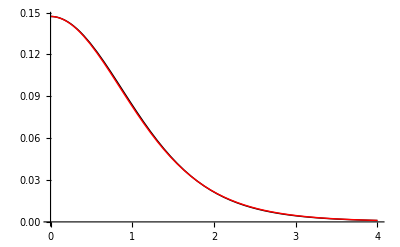

```mathematica
Plot[{MGProf[r,1,.5],MoffM2[r,Sqrt[MMEVG2[1,0,0,0.5]],3.908656383171676]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

```mathematica
MEProf[r_,Rhwhm_,Ref_]:=NIntegrate[MoffM2[Sqrt[r^2+rt^2-2 r rt Cos[th]],HWHM2R35 Rhwhm ,3.5]2  rt EProf[rt,Ref],{th,0, Pi},{rt,0,5Ref},AccuracyGoal->3]
```

```mathematica
ME0[Rhwhm_,Ref_]:=NIntegrate[2 Pi r MoffM2[r,HWHM2R35 Rhwhm ,3.5] EProf[r,Ref],{r,0,5Ref},AccuracyGoal->3]
```

```mathematica
ME0[1,.5]
```

0.131901

```mathematica
MEProf[0,1,.5]
```

0.131903

```mathematica
(2 Pi ME0[1,.5]MMEVG2[1,0.5,0,0]-1)/( Pi ME0[1,.5]MMEVG2[1,0.5,0,0]-1)  
(* value of β to give right central value and M2  *)
```

4.07465

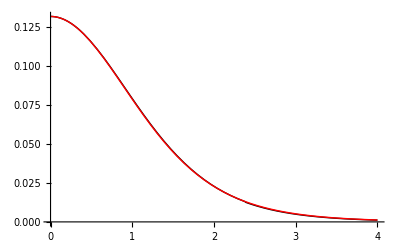

```mathematica
Plot[{MEProf[r,1,.5],MoffM2[r,Sqrt[MMEVG2[1,0.5,0,0]],4.074645205109686]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

```mathematica
MVProf[r_,Rhwhm_,Ref_]:=NIntegrate[MoffM2[Sqrt[r^2+rt^2-2 r rt Cos[th]],1.7446920204827057Rhwhm ,3.5]2  rt VProf[rt,Ref],{th,0, Pi},{rt,0,20Ref},AccuracyGoal->5]
```

```mathematica
MV0[Rhwhm_,Ref_]:=NIntegrate[2 Pi r MoffM2[r,1.7446920204827057Rhwhm ,3.5] VProf[r,Ref],{r,0,20Ref},AccuracyGoal->5]
```

```mathematica
(2 Pi MV0[1,.5]MMEVG2[1,0,0.5,0]-1)/( Pi MV0[1,.5]MMEVG2[1,0,0.5,0]-1)
(* value of β to give right central value and M2  *)
```

2.48606

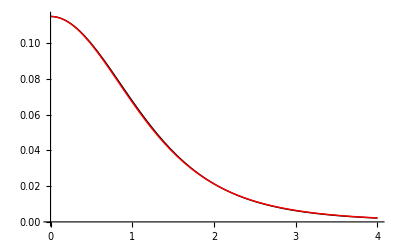

```mathematica
Plot[{MVProf[r,1,.5],MoffM2[r,Sqrt[MMEVG2[1,0,0.5,0]],2.4860561415194153]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

```mathematica
MV0[1,.5]
```

0.114983

```mathematica
MVProf[0,1.,.5]
```

0.114983

```mathematica
(2 Pi MV0[1,1]MMEVG2[1,0,1,0]-1)/( Pi MV0[1,1]MMEVG2[1,0,1,0]-1)
(* value of β to give right central value and M2  *)
```

2.17854

```mathematica
q1
```

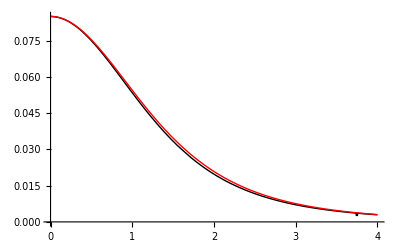

```mathematica
Plot[{MVProf[r,1,1],MoffM2[r,Sqrt[MMEVG2[1,0,1,0]],2.178536198176785]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

```mathematica
(*  start aperture stuff   *)
```

```mathematica
PlateScDESP=56.73   (* um/arcsec *)
```

56.73

```mathematica
Rsee[FWHMsite_,λ_,AM_]:=FWHMsite/2   (λ/500)^-0.2  AM^(3/5)
(* median HWHM seeing at any Air Mass and wavelength *)
```

```mathematica
FWHMCT=0.75
```

0.75

```mathematica
FWHMbyrms=2 Sqrt[Log[4.]] / Sqrt[2]  (* FWHM=1.665 rms radius for Gaussian *)
```

1.66511

```mathematica
(* Relg=0.29 *) (* nominal ELG reff val at i=23.5, SK's formula *)
```

```mathematica
(* Relgmax=0.375 *) (* Steve's cut, rescaled to i=23.5 *)
```

```mathematica
Relg=0.4 (* agrees better with Steph's target list *)
```

0.4

```mathematica
Relgmax=0.5 (* so quite tightly trimmed *)
```

0.5

```mathematica
Rlrg=0.35
```

0.35

```mathematica
Rlrgmax=0.5
```

0.5

```mathematica
(* Rrmsfix=Sqrt[16.5^2 - 9.3^2-10^2 -1^2] *)(* SK's UCL meeting numbers *)
```

```mathematica
FWHMfixDS=0.5
```

0.5

```mathematica
Rrmsfix=FWHMfixDS*PlateScDESP /FWHMbyrms (* Everything except atmospheric seeing and zemax spot size. Includes guiding errors, dome/mirror seeing, imperfect optics etc. Gives i-band median zenith DIQ = 0.9" with DECam *)
```

17.0349

```mathematica
DefocMH=20
```

20

```mathematica
ApEta[Rseehm_,RE_,RV_,Rrmstot_,RAp_]:=NIntegrate[2 Pi r MoffM2[r,Sqrt[MMEVG2[Rseehm,RE,RV,Rrmstot/PlateScDESP]],BetaMEVG0[Rseehm,RE,RV,Rrmstot/PlateScDESP]],{r,0,RAp}]
```

```mathematica
ApEtavsrms[rms_]:=NIntegrate[2 Pi r MoffM2[r,Sqrt[MMEVG2[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+rms^2]/PlateScDESP]],BetaMEVG0[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+rms^2]/PlateScDESP]],{r,0,1.8/2}]
```

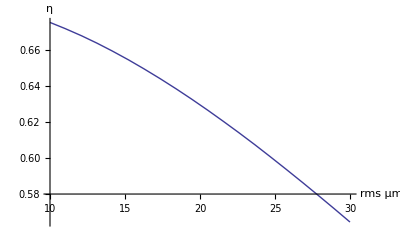

```mathematica
Plot[ApEtavsrms[rms],{rms,10,30},PlotStyle->Thick,AxesLabel->  {rms (μm),η},AxesStyle->Directive[Thick,14, Bold],PlotPoints->20,MaxRecursion->0]
```

```mathematica
AMloss[λ_]:=Switch[λ,
350,0.595,
370,0.614,
400,0.679,
450,0.770,
500,0.824,
550,0.846,
600,0.855,
650,0.883,
700,0.917,
750,0.943,
800,0.963,
850,0.976,
900,0.985,
950,0.991,
1000,0.993]
```

```mathematica
SNrms[λ_,dfib_,Rg_,AM_,Rrms_]:=AMloss[λ]^AM NIntegrate[ 2  Pi r MoffM2[r,Sqrt[MMEVG2[Rsee[FWHMCT,λ,AM],Rg,0,Sqrt[Rrmsfix^2+Rrms^2]/PlateScDESP]],BetaMEVG0[Rsee[FWHMCT,λ,AM],Rg,0,Sqrt[Rrmsfix^2+Rrms^2]/PlateScDESP]],{r,0,dfib/2}]/(Sqrt[AM] dfib)                  (* S/N ratio, assumes sky-limited *)
```

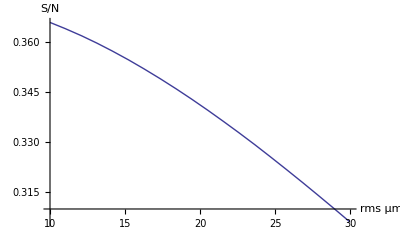

```mathematica
Plot[SNrms[850,1.8,Relg,1.0,Rrms],{Rrms,10,30},PlotStyle->Thick,AxesLabel->  {rms (μm),"S/N"},AxesStyle->Directive[Thick,14, Bold],PlotPoints->20,MaxRecursion->0]
```

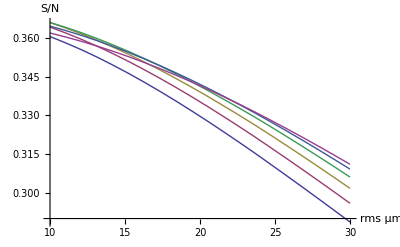

```mathematica
Plot[{SNrms[850,1.5,Relg,1.0,Rrms],SNrms[850,1.6,Relg,1.0,Rrms],SNrms[850,1.7,Relg,1.0,Rrms],SNrms[850,1.8,Relg,1.0,Rrms],SNrms[850,1.9,Relg,1.0,Rrms],SNrms[850,2.0,Relg,1.0,Rrms]},{Rrms,10,30},PlotStyle->Thick,AxesLabel->  {rms (μm),"S/N"},PlotPoints->20,MaxRecursion->0,AxesStyle->Directive[Thick,14, Bold]]
```

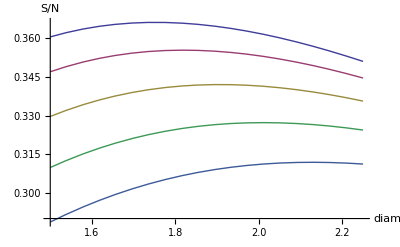

```mathematica
Plot[{SNrms[850,dfib,Relg,1.0,10],SNrms[850,dfib,Relg,1.0,15],SNrms[850,dfib,Relg,1.0,20],SNrms[850,dfib,Relg,1.0,25],SNrms[850,dfib,Relg,1.0,30]},{dfib,1.5,2.25},PlotStyle->Thick,AxesLabel->  {diam,"S/N"},PlotPoints->20,MaxRecursion->0,AxesStyle->Directive[Thick,14, Bold]]
```

```mathematica
RMSSpot7[λ_]=Switch[λ,
350,25.8,
370,24.7,
400,23.0,
450,19.9,
500,15.7,
550,13.3,
600,13.4,
650,13.4,
700,13.7,
750,14.1,
800,14.4,
850,15.3,
900,15.9,
950,16.6,
1000,17.3,
1050,18.1] 
(* DESpec7 spot sizes *)
```

Switch[λ,
350,25.8,
370,24.7,
400,23.,
450,19.9,
500,15.7,
550,13.3,
600,13.4,
650,13.4,
700,13.7,
750,14.1,
800,14.4,
850,15.3,
900,15.9,
950,16.6,
1000,17.3,
1050,18.1]

```mathematica
Ropt7[λ_]:=Sqrt[(Rrmsfix^2+RMSSpot7[λ]^2)]/PlateScDESP
(* Rrms in arcsec, includes rms=Rrmsfixum for surface and alignment errors *)
```

```mathematica
SN7[λ_,dfib_,Rg_,AM_]:=NIntegrate[ 2  Pi r MoffM2[r,Sqrt[MMEVG2[Rsee[FWHMCT,λ,AM],Rg,0,Ropt7[λ]]],BetaMEVG0[Rsee[FWHMCT,λ,AM],Rg,0,Ropt7[λ]]],{r,0,dfib/2}]/dfib 
(* S/N ratio assumes sky-limited *)
```

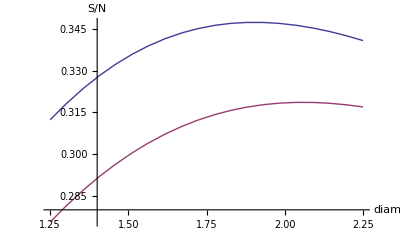

```mathematica
P7850g=Plot[{SN7[850,dfib,Relg,1.2],SN7[850,dfib,Relgmax,1.2]},{dfib,1.25,2.25},PlotStyle->Thick,AxesLabel->  {diam,"S/N"},AxesStyle->Directive[Thick,14, Bold],PlotPoints->20,MaxRecursion->0]
(* S/N vs fiber size for elg and elgmax at AM=1.2 *)
```

```mathematica
Quiet[FindMaximum[SN7[850,dfib,Relg,1.2],{dfib,1.5}]]
```

{0.347318,{dfib→1.90301}}

```mathematica
Quiet[FindMaximum[SN7[850,dfib,Relgmax,1.2],{dfib,1.5}]]
```

{0.318598,{dfib→2.05851}}

```mathematica
(* now off-center apertures *)
```

```mathematica
Frac[r1_,r2_,del_]:=If[del==0,0,Re[ArcCos[Max[-1,Min[1,(r1^2+del^2-r2^2 )/(2r1 Abs[del])]]]/Pi]]
```

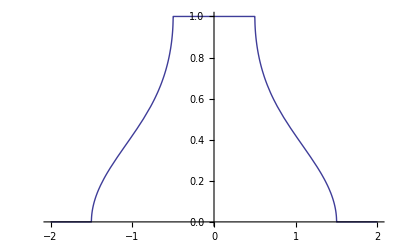

```mathematica
Plot[Frac[0.5,1,del],{del,-2,2}]
```

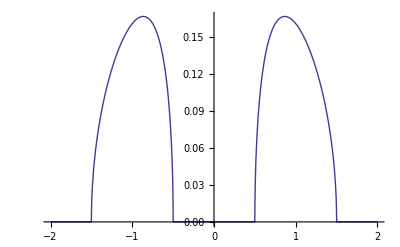

```mathematica
Plot[Frac[1,0.5,del],{del,-2,2}]
```

```mathematica
Frac[1,1,1]
```

1/3

```mathematica
ApEtad[R_,β_,RAp_,del_]:=If[del==0,NIntegrate[2 Pi r MoffM2[r,R,β],{r,0,RAp}],NIntegrate[2 Pi r Frac[r,RAp,del]MoffM2[r,R,β],{r,0,Infinity}]]
```

```mathematica
ApEtad[1,3.5,1,0]
```

0.721145

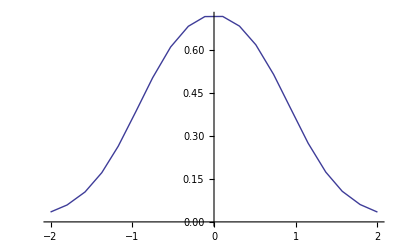

```mathematica
Plot[ApEtad[1,3.5,1,del],{del,-2,2},PlotPoints->20,MaxRecursion->0]
```

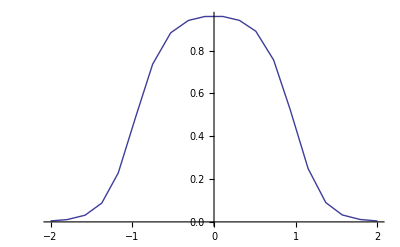

```mathematica
Plot[ApEtad[.5,3.5,1,del],{del,-2,2},PlotPoints->20,MaxRecursion->0]
```

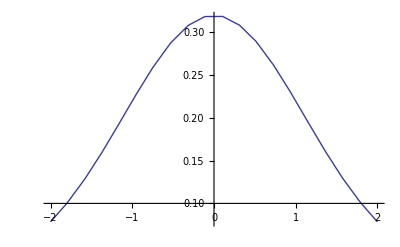

```mathematica
Plot[ApEtad[2,3.5,1,del],{del,-2,2},PlotPoints->20,MaxRecursion->0]
```

```mathematica
ApEtadG[Rrms_,RAp_,del_]:=If[del==0,NIntegrate[2 Pi r GProf[r,Rrms],{r,0,RAp}],NIntegrate[2 Pi r Frac[r,RAp,del]GProf[r,Rrms],{r,0,Infinity}]]
```

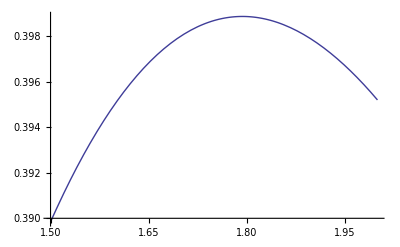

```mathematica
Plot[ApEtadG[0.8,DAp/2,0]/DAp,{DAp,1.5,2}]
```

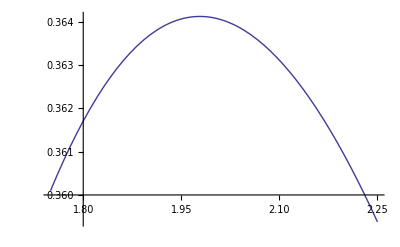

```mathematica
Plot[ApEtadG[0.8,DAp/2,20/56.73]/DAp,{DAp,1.75,2.25}]
```

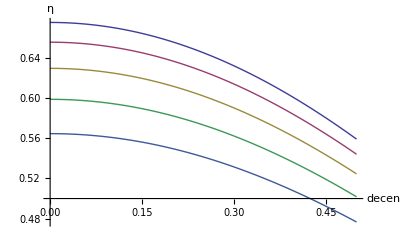

```mathematica
Plot[{ApEtad[Sqrt[MMEVG2[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+10^2]/PlateScDESP]],BetaMEVG0[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+10^2]/PlateScDESP],1.8/2,del],ApEtad[Sqrt[MMEVG2[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+15^2]/PlateScDESP]],BetaMEVG0[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+15^2]/PlateScDESP],1.8/2,del],ApEtad[Sqrt[MMEVG2[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+20^2]/PlateScDESP]],BetaMEVG0[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+20^2]/PlateScDESP],1.8/2,del],ApEtad[Sqrt[MMEVG2[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+25^2]/PlateScDESP]],BetaMEVG0[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+25^2]/PlateScDESP],1.8/2,del],ApEtad[Sqrt[MMEVG2[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+30^2]/PlateScDESP]],BetaMEVG0[Rsee[FWHMCT,850,1],Relg,0,Sqrt[Rrmsfix^2+30^2]/PlateScDESP],1.8/2,del]},{del,0,0.5},PlotStyle->Thick,AxesLabel->  {decen,η},AxesStyle->Directive[Thick,14, Bold]]
(* aperture efficiency vs decentering and rms *)
```

```mathematica
(*  differential refraction , actually for LaSilla. T=11.5 C,RH=44.2%,P=772.2mbar *)
```

```mathematica
ZD[AM_]:=ArcCos[1/AM]
```

```mathematica
TC=11.5
```

11.5

```mathematica
T=273.16+TC
```

284.66

```mathematica
PS=-10474.0+116.43 T-0.43284 T^2+0.00053840 T^3
```

14.3051

```mathematica
RH=.442
```

0.442

```mathematica
P2=RH PS
```

6.32284

```mathematica
P1=772.2
```

772.2

```mathematica
D1=P1/T (1.0+P1 (57.90  10^-8-(9.3250 10^-4/T)+(0.25844/T^2)))
```

2.71374

```mathematica
D2=P2/T(1.0+P2 (1.0+3.7 10^-4P2)(-2.37321 10^-3+(2.23366/T)-(710.792/T^2)+(7.75141 10^4/T^3)))
```

0.0222207

```mathematica
N1[λ_]:=1.0 10^-8((2371.34+683939.7/(130-1/λ^2)+4547.3/(38.9-1/λ^2)) D1+ (6487.31+58.058/λ^2-0.71150/λ^4+0.08851/λ^6) D2)
```

```mathematica
N1[.5]
```

0.000216684

```mathematica
DR[λ_,λ0_,AM_]:=Tan[ZD[AM]](N1[λ0/1000]-N1[λ/1000]) 206264.8
```

```mathematica
DR[600,500,1.1]
```

0.146518

```mathematica
DR[350,400,1.2]
```

-0.358024

```mathematica
DR[820,800,1.4]
```

0.0186451

```mathematica
ADCloss[λ_]:=Switch[λ,
350,0.78,
370,.863,
400,.941,
450,.935,
500,.931,
550,.936,
600,.942,
650,.946,
700,.957,
750,.962,
800,.966,
850,.963,
900,.959,
950,.955,
1000,.951,
1050,0.947] 
(* nominal throughput for ADC as in SK's V3. last number 0.947 estimated*)
```

```mathematica
AMloss[λ_]:=Switch[λ,
350,0.595,
370,0.614,
400,0.679,
450,0.770,
500,0.824,
550,0.846,
600,0.855,
650,0.883,
700,0.917,
750,0.943,
800,0.963,
850,0.976,
900,0.985,
950,0.991,
1000,0.993]
(* CTIO extinction losses per air mass *)
```

```mathematica
SkyBr[λ_,AM_]:=AM AMloss[λ]^(AM-1)  
(* model of Patat, Sanchez, assuming all airglow *)
```

```mathematica
FAM[AM_]:=Switch[AM,
1.05,0.333,
1.15,0.314,
1.25,0.224,
1.35,0.09,
1.45,0.024,
1.55,0.01,
1.65,0.001,
1.75,0.001,
1.85,0.001,
1.95,0,
2.05,0]  
(* SK's SDSS AM distn. deleted 2.05 field, special request! *)
```

```mathematica
ApEtaAll[λ_,λ0_,FWHMsite_,AM_,Decent_,RmsSpot_,FWHMFix_,DDefoc_,PlateSc_,DAp_,RE_,RV_]:=ApEtad[Sqrt[MMEVG2[Rsee[FWHMsite,λ,AM],RE,RV,Sqrt[(FWHMFix/FWHMbyrms)^2+(RmsSpot/PlateSc)^2+(DDefoc/PlateSc)^2/8]]],BetaMEVG0[Rsee[FWHMsite,λ,AM],RE,RV,Sqrt[(FWHMFix/FWHMbyrms)^2+(RmsSpot/PlateSc)^2+(DDefoc/PlateSc)^2/8]],DAp/2,Sqrt[(Decent/PlateSc)^2+DR[λ,λ0,AM]^2]]
(* ApEtaAll is general purpose aperture loss function
 λ,λ0 are target wavelength and fiber-centering wavelength
AM is airmass
Decent is decentering in um (added in quadrature to differential refraction)
RmsSpot is spot size from ZEMAX, assumed Gaussian
 FWHMFix is addition for dome seeing, guiding, alignment etc
DDefoc is defocus diameter = axial dist/f-number
PlateSc is plate scale (um/arcsec)
DAp is fiber diamater
RE is effective radius for exponential profile
RV is effective radius for deVaucouleurs profile
*)
```

```mathematica
ApEtaAll[350,400,FWHMCT,1.0,10,25,0.5,20,PlateScDESP,1.76,0,0]
```

0.643274

```mathematica
ApEtaAll[850,850,FWHMCT,1.0,10,25,0.5,20,PlateScDESP,1.76,Relg,0]
```

0.56411

```mathematica
ApEtaAll[800,800,FWHMCT,1.0,10,25,0.5,20,PlateScDESP,1.76,0,Rlrg]
```

0.475774

```mathematica
ApEtaDR7[λ_,λ0_,AM_,rfib_,RE_,RV_]:=ApEtaAll[λ,λ0,FWHMCT,AM,10,RMSSpot7[λ],0.5,20,PlateScDESP,2 rfib,RE,RV]
```

```mathematica
(* Aperture efficiencies at zenith for 1.8" fibers *)
```

```mathematica
Do[Print[λ," ",ApEtaDR7[λ,400,1.0,1.8/2,0,0]],{λ,{350,370,400,450,500,550}}]
(* qsos *)
```

350 0.652451

370 0.664674

400 0.682762

450 0.712861

500 0.746264

550 0.765738

```mathematica
Do[Print[λ," ",ApEtaDR7[λ,λ,1.0,1.8/2,0,0]],{λ,{550,600,650,700,750,800,850,900,1000,1050}}]
(* PS in red for throughput plot *)
```

550 0.765738

600 0.771651

650 0.777432

700 0.781213

750 0.783998

800 0.786866

850 0.786062

900 0.786429

1000 0.784745

1050 0.782648

```mathematica
Do[Print[λ," ",ApEtaDR7[λ,λ,1.0,1.8/2,Relg,0]],{λ,{550,600,650,700,750,800,850,900,1000,1050}}]
(* elgs *)
```

550 0.617557

600 0.621938

650 0.62625

700 0.628989

750 0.630941

800 0.632995

850 0.632087

900 0.632163

1000 0.63043

1050 0.628589

```mathematica
(* now AM=1.2 *)
```

```mathematica
Do[Print[λ," ",ApEtaDR7[λ,400,1.0,1.8/2,0,0]],{λ,{350,370,400,450,500,550}}]
(* qsos *)
```

350 0.652451

370 0.664674

400 0.682762

450 0.712861

500 0.746264

550 0.765738

```mathematica
Do[Print[λ," ",ApEtaDR7[λ,λ,1.2,1.8/2,Relg,0]],{λ,{550,600,650,700,750,800,850,900,1000,1050}}]
(* elgs *)
```

550 0.585765

600 0.590682

650 0.595454

700 0.598718

750 0.601205

800 0.603718

850 0.603481

900 0.604077

1000 0.603378

1050 0.602106

```mathematica
(* end of aperture stuff *)
```

```mathematica
SSpeedAll[λ_,λ0_,FWHMsite_,AM_,Decent_,RmsSpot_,FWHMFix_,DDefoc_,PlateSc_,DAp_,RE_,RV_,Res1_,VSig_]:=(AMloss[λ]^AM ApEtaAll[λ,λ0,FWHMsite,AM,Decent,RmsSpot,FWHMFix,DDefoc,PlateSc,DAp,RE,RV]/DAp)^2  /(SkyBr[λ,AM]Sqrt[1+((300000 DAp/Res1)/(2.355 VSig))^2])
```

```mathematica
(* survey speed including extinction, sky noise, spectral resolution effects *)
```

```mathematica
Plot[SSpeedAll[850,850,FWHMCT,AM,10,RMSSpot7[850],FWHMfixDS,DefocMH,PlateScDESP,1.8,Relg,0,6000,80],{AM,1.0,2},PlotPoints->10,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Air Mass","Speed"},AxesStyle->Directive[Thick,14, Bold]]
(* survey speed vs air mass for elgs *)
```

```mathematica
Plot[SSpeedAll[350,400,FWHMCT,AM,10,RMSSpot7[350],FWHMfixDS,DefocMH,PlateScDESP,1.8,Relg,0,7500,20],{AM,1.0,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Air Mass","Speed"},AxesStyle->Directive[Thick,14, Bold]]
(* survey speed vs air mass for qsos at 350nm but centred at 400 *)
```

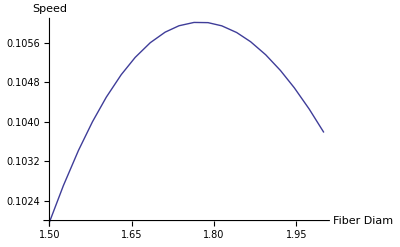

```mathematica
Plot[SSpeedAll[850,850,FWHMCT,1.0,10,RMSSpot7[850],FWHMfixDS,DefocMH,PlateScDESP,DAp,Relg,0,6000,80],{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Speed"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey speed vs fiber size for elgs at zenith *)
```

```mathematica
Quiet[NMaximize[{SSpeedAll[850,850,FWHMCT,1.0,10,RMSSpot7[850],FWHMfixDS,DefocMH,PlateScDESP,DAp,Relg,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* optimal vs fiber size for elgs at zenith *)
```

{0.106024,{DAp→1.77446}}

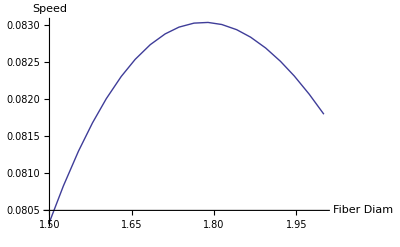

```mathematica
Plot[SSpeedAll[800,800,FWHMCT,1.0,10,RMSSpot7[800],FWHMfixDS,DefocMH,PlateScDESP,DAp,0,Rlrg,6000,200],{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Speed"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey speed vs fiber size for lrgs at zenith *)
```

```mathematica
Quiet[NMaximize[{SSpeedAll[800,800,FWHMCT,1.0,10,RMSSpot7[800],FWHMfixDS,DefocMH,PlateScDESP,DAp,0,Rlrg,6000,200],DAp>1&&DAp<2},{DAp}]]
(* optimal fiber size for lrgs at zenith *)
```

{0.0830413,{DAp→1.78223}}

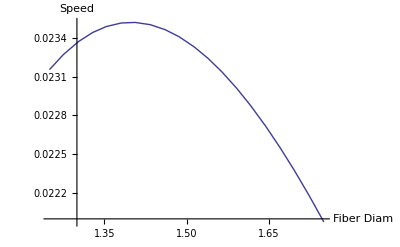

```mathematica
Plot[SSpeedAll[350,410,FWHMCT,1.0,10,RMSSpot7[350],FWHMfixDS,DefocMH,PlateScDESP,DAp,0,0,6000,20],{DAp,1.25,1.75},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Speed"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey speed vs fiber size for qso at 350nm zenith *)
```

```mathematica
Quiet[NMaximize[{SSpeedAll[350,410,FWHMCT,1.0,10,RMSSpot7[350],FWHMfixDS,DefocMH,PlateScDESP,DAp,0,0,6000,20],DAp>1&&DAp<2},{DAp}]]
(*  optimal fiber size for qso at 350nm zenith *)
```

{0.0235206,{DAp→1.39901}}

```mathematica
(* now find total survey time for SDSS AM distn *)
```

```mathematica
STime[λ_,λ0_,FWHMsite_,Decent_,RmsSpot_,FWHMFix_,DDefoc_,PlateSc_,DAp_,RE_,RV_,Res1_,VSig_]:=Sum[FAM[AM]/SSpeedAll[λ,λ0,FWHMsite,AM,Decent,RmsSpot,FWHMFix,DDefoc,PlateSc,DAp,RE,RV,Res1,VSig],{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
```

```mathematica
STimeAM01[λ_,λ0_,FWHMsite_,Decent_,RmsSpot_,FWHMFix_,DDefoc_,PlateSc_,DAp_,RE_,RV_,Res1_,VSig_]:= Sum[FAM[AM]/SSpeedAll[λ,λ0,FWHMsite,AM+0.1,Decent,RmsSpot,FWHMFix,DDefoc,PlateSc,DAp,RE,RV,Res1,VSig],{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
(* survey time for SDSS AM+0.1 distn *)
```

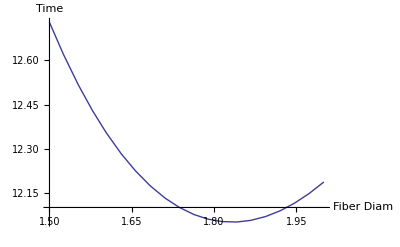

```mathematica
Plot[STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relg,0,6000,80],{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for elgs *)
```

```mathematica
temp=Quiet[NMinimize[{STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relg,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* optimal fiber size for elgs *)
```

{12.0502,{DAp→1.83274}}

```mathematica
DAp1=DAp/.temp[[2]]
```

1.83274

```mathematica
Time1=temp[[1]]
```

12.0502

```mathematica
STimeAM01[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp1,Relg,0,6000,80]/Time1
(* AM+0.1 time penalty *)
```

1.13726

```mathematica
Quiet[NMinimize[{STimeAM01[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relg,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* AM+0.1 effect on optimal fiber size *)
```

{13.699,{DAp→1.8629}}

```mathematica
STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp1,Relgmax,0,6000,80]/Time1
(* elgmax time penalty *)
```

1.20426

```mathematica
Quiet[NMinimize[{STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relgmax,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* elgmax effect on optimal fiber size *)
```

{14.4253,{DAp→1.95577}}

```mathematica
STime[850,850,.9,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp1,Relg,0,6000,80]/Time1
(* 0.9" seeing time penalty *)
```

1.20296

```mathematica
Quiet[NMinimize[{STime[850,850,.9,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relg,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* 0.9" seeing effect on optimal fiber size *)
```

{14.4071,{DAp→1.95754}}

```mathematica
STime[850,850,.75,10,20,FWHMfixDS,DefocMH,56.73,DAp1,Relg,0,6000,80]/Time1
(* 20um rms spot time penalty *)
```

1.07483

```mathematica
Quiet[NMinimize[{STime[850,850,.75,10,20,FWHMfixDS,DefocMH,56.73,DAp,Relg,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* 20um rms spot effect on optimal fiber size *)
```

{12.9296,{DAp→1.89712}}

```mathematica
Quiet[NMinimize[{STime[850,850,.75,10,RMSSpot7[850],.4,DefocMH,56.73,DAp,Relg,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* 0.4 fixed error on optimal fiber size *)
```

{11.4955,{DAp→1.79032}}

```mathematica
STime[850,850,.75,10,RMSSpot7[850],.4,DefocMH,56.73,DAp1,Relg,0,6000,80]/Time1
(* 0.4 fixed error time benefit *)
```

0.954723

```mathematica
Quiet[NMinimize[{STime[850,850,.75,20,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relg,0,6000,80],DAp>1&&DAp<2},{DAp}]]
(* 20um decentering error effect on optimal fiber size *)
```

{13.6298,{DAp→1.95956}}

```mathematica
STime[850,850,.75,20,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp1,Relg,0,6000,80]/Time1
(* 20um decentering error time penalty *)
```

1.13858

```mathematica
Quiet[NMinimize[{STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relg,0,7500,80],DAp>1&&DAp<2},{DAp}]]
(* higher resn effect on optimal fiber size *)
```

{11.6205,{DAp→1.8718}}

```mathematica
STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp1,Relg,0,7500,80]/Time1
(* higher resn time benefit *)
```

0.964948

```mathematica
(*  end elg tests *)
```

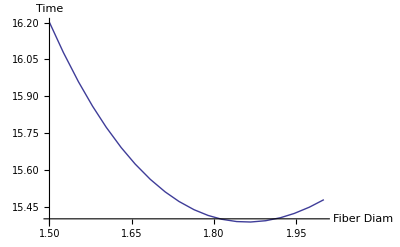

```mathematica
Plot[STime[800,800,.75,10,RMSSpot7[800],FWHMfixDS,DefocMH,56.73,DAp,0,Rlrg,6000,200],{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for lrgs *)
```

```mathematica
Quiet[NMinimize[{STime[800,800,.75,10,RMSSpot7[800],FWHMfixDS,DefocMH,56.73,DAp,0,Rlrg,6000,200],DAp>1&&DAp<2},{DAp}]]
(* optimal fiber size for lrgs *)
```

{15.3869,{DAp→1.86086}}

```mathematica
Quiet[NMinimize[{STimeAM01[800,800,.75,10,RMSSpot7[800],FWHMfixDS,DefocMH,56.73,DAp,0,Rlrg,6000,200],DAp>1&&DAp<2},{DAp}]]
(* AM+0.1 time penalty for lrgs *)
```

{17.4748,{DAp→1.90117}}

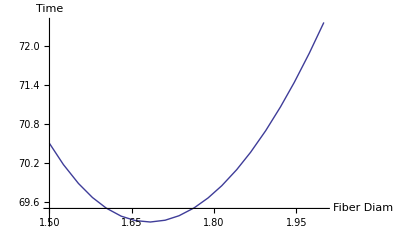

```mathematica
Plot[STime[350,400,.75,10,RMSSpot7[350],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for qsos at 350nm *)
```

```mathematica
Quiet[NMinimize[{STimeAll[350,400,.75,10,RMSSpot7[350],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],DAp>1&&DAp<2},{DAp}]]
(* optimal fiber size for qsos at 350nm *)
```

{69.2915,{DAp→1.68187}}

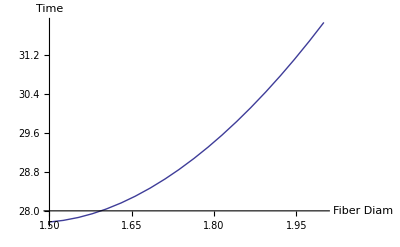

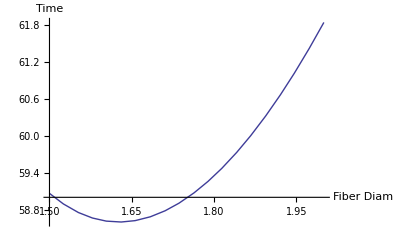

```mathematica
Plot[STime[450,400,.75,10,RMSSpot7[450],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for qsos at 450nm *)
```

```mathematica
Quiet[NMinimize[{STime[450,400,.75,10,RMSSpot7[450],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],DAp>1&&DAp<2},{DAp}]]
(* optimal fiber size for qsos at 450nm *)
```

{27.7595,{DAp→1.47388}}

{58.5978,{DAp→1.62684}}

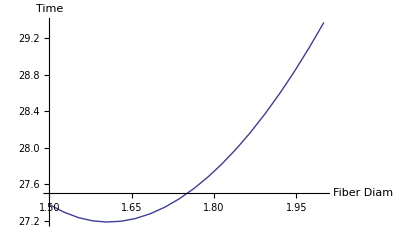

```mathematica
Plot[STime[500,400,.75,10,RMSSpot7[500],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for qsos at 500nm *)
```

```mathematica
Quiet[NMinimize[{STime[500,400,.75,10,RMSSpot7[500],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],DAp>1&&DAp<2},{DAp}]]
(* optimal fiber size for qsos at 500nm *)
```

{27.188,{DAp→1.60716}}

```mathematica
(*  Now ADC stuff *)
STimeADC[λ_,FWHMsite_,Decent_,RmsSpot_,FWHMFix_,DDefoc_,PlateSc_,DAp_,RE_,RV_,Res1_,VSig_]:=Sum[FAM[AM]/(SSpeedAll[λ,λ,FWHMsite,AM,Decent,RmsSpot,FWHMFix,DDefoc,PlateSc,DAp,RE,RV,Res1,VSig]ADCloss[λ]),{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
```

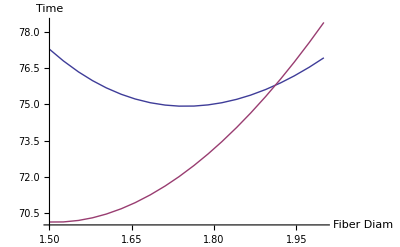

```mathematica
Plot[{STime[350,410,.75,10,RMSSpot7[350],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],STimeADC[350,.75,10,RMSSpot7[350],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20]},{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for qsos at 350nm *)
```

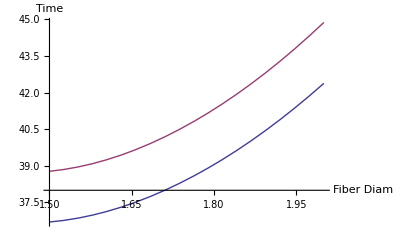

```mathematica
Plot[{STimeAll[400,410,.75,10,RMSSpot7[400],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],STimeAllADC[400,.75,10,RMSSpot7[400],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20]},{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for qsos at 350nm *)
```

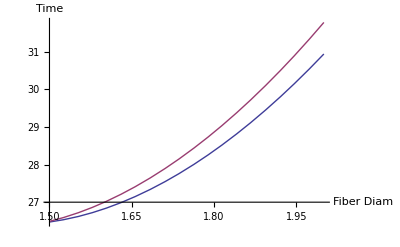

```mathematica
Plot[{STimeAll[450,410,.75,10,RMSSpot7[450],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],STimeAllADC[450,.75,10,RMSSpot7[450],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20]},{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for qsos at 350nm *)
```

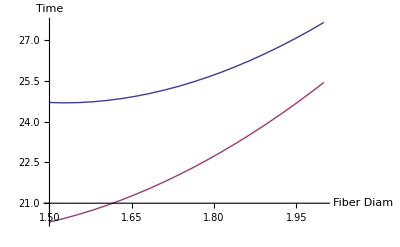

```mathematica
Plot[{STimeAll[500,410,.75,10,RMSSpot7[500],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],STimeAllADC[500,.75,10,RMSSpot7[500],FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20]},{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for qsos at 350nm *)
```

```mathematica
(* BigBOSS stuff *)
```

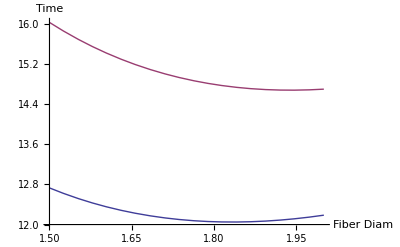

```mathematica
Plot[{STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,DAp,Relg,0,6000,80],STimeADC[850,.9,10,RMSSpot7[850],FWHMfixDS,0,56.73,DAp,Relg,0,6000,80]},{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for elgs *)
```

```mathematica
Quiet[NMinimize[{STimeADC[850,.9,10,RMSSpot7[850],FWHMfixDS,0,56.73,DAp,Relg,0,6000,80],DAp<2.5&&DAp>1},DAp]]
```

{14.6738,{DAp→1.93909}}

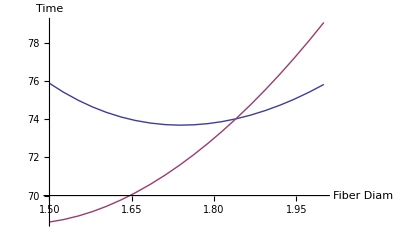

```mathematica
Plot[{STime[350,410,.75,10,25,FWHMfixDS,DefocMH,56.73,DAp,0,0,7500,20],STimeADC[350,.9,10,17.5/1.5,FWHMfixDS,0,56.73,DAp,0,0,7500,20]},{DAp,1.5,2},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {"Fiber Diam","Time"},AxesStyle->Directive[Thick,14, Bold]]
(*  survey time vs fiber size for elgs *)
```

```mathematica
STime[850,850,.75,10,RMSSpot7[850],FWHMfixDS,DefocMH,56.73,1.84,Relg,0,6000,80]/STimeADC[850,.9,10,RMSSpot7[850],FWHMfixDS,0,56.73,1.45,Relg,0,6000,80]
```

0.734683

```mathematica
STime[800,800,.75,10,RMSSpot7[800],FWHMfixDS,DefocMH,56.73,1.84,0,Rlrg,6000,200]/STimeADC[800,.9,10,RMSSpot7[800],FWHMfixDS,0,56.73,1.45,0,Rlrg,6000,200]
```

0.745059

```mathematica
STime[350,400,.75,10,RMSSpot7[350],FWHMfixDS,DefocMH,56.73,1.84,0,0,7500,20]/STimeADC[350,.9,10,17.5/4.5,FWHMfixDS,0,56.73,1.45,0,0,7500,20]
```

1.10278

```mathematica
STime[400,400,.75,10,RMSSpot7[400],FWHMfixDS,DefocMH,56.73,1.84,0,0,7500,20]/STimeADC[400,.9,10,17.5/4.5,FWHMfixDS,0,56.73,1.45,0,0,7500,20]
```

1.05651

```mathematica
STime[450,400,.75,10,RMSSpot7[450],FWHMfixDS,DefocMH,56.73,1.84,0,0,7500,20]/STimeADC[450,.9,10,17.5/4.5,FWHMfixDS,0,56.73,1.45,0,0,7500,20]
```

1.09589

```mathematica
STime[500,400,.75,10,RMSSpot7[500],FWHMfixDS,DefocMH,56.73,1.84,0,0,7500,20]/STimeADC[500,.9,10,17.5/4.5,FWHMfixDS,0,56.73,1.45,0,0,7500,20]
```

1.23723

```mathematica
(* 4MOST stuff *)
```

```mathematica
FWHMsee500=0.7
```

0.7

```mathematica
ApEtaDR7[500,500,1.2,1.5/2,0,0]
```

0.583611

```mathematica
ApEta[0.35,0,0,20,0.75]
```

0.719619

```mathematica
ApEta[0.35,0,0,Sqrt[20^2+(0.707*50/(2*3.24))^2],0.75]/ApEta[0.35,0,0,20,0.75]
```

0.990045

```mathematica
ApEta[0.35,0,0,Sqrt[20^2+(0.707*100/(2*3.24))^2],0.75]/ApEta[0.35,0,0,20,0.75]
```

0.960937

```mathematica
ApEta[0.35,0,0,Sqrt[20^2+(0.707*170/(2*3.24))^2],0.75]/ApEta[0.35,0,0,20,0.75]
```

0.892706

```mathematica
ApEta[0.35,0,0,Sqrt[20^2+(0.707*200/(2*3.24))^2],0.75]/ApEta[0.35,0,0,20,0.75]
```

0.856011

```mathematica
(* Gaussian test *)
```

```mathematica
SN[R_]:= Integrate[r Exp[-r^2],{r,0,R}] /R
```

```mathematica
FindRoot[SN'[R]==0,{R,1}]
```

{R→1.12091}

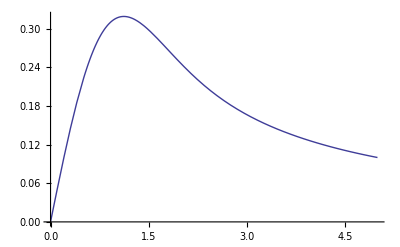

```mathematica
Plot[SN[R],{R,0,5}]
```

```mathematica
Integrate[r ^3 Exp[-r^2],{r,0,Infinity}]/Integrate[r Exp[-r^2],{r,0,Infinity}]
```

1